1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
MUL=1;
jj =0;
mJ=0;
pi="-";
```

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.00391158+2.67252×10^-6 ⅈ,0.00468408+3.82512×10^-6 ⅈ,0.00483113+7.99272×10^-6 ⅈ,0.00354194+0.000010283 ⅈ,0.00144335+0.0000125904 ⅈ,0.000421825+0.0000134964 ⅈ,-0.000456094+0.000014208 ⅈ,-0.000844849+0.000014508 ⅈ,-0.00118413+0.0000147636 ⅈ,-0.00132604+0.000014868 ⅈ,-0.00142375+0.00001494 ⅈ,-0.00152295+0.000015012 ⅈ,-0.00159396+0.0000150636 ⅈ,-0.00162896+0.0000150888 ⅈ,-0.00164886+0.0000151032 ⅈ,-0.00165856+0.0000151104 ⅈ,-0.00166446+0.000015114 ⅈ,-0.00166716+0.0000151164 ⅈ,-0.00166836+0.0000151176 ⅈ,-0.00166916+0.0000151176 ⅈ,-0.00166966+0.0000151176 ⅈ},«19»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.00391136+2.67252×10^-6 ⅈ,0.00468377+3.82512×10^-6 ⅈ,0.00483047+7.99272×10^-6 ⅈ,0.00354109+0.000010283 ⅈ,0.00144231+0.0000125904 ⅈ,0.000420712+0.0000134964 ⅈ,-0.000457266+0.000014208 ⅈ,-0.000846046+0.000014508 ⅈ,-0.00118535+0.0000147636 ⅈ,-0.00132727+0.000014868 ⅈ,«1»,-0.00152419+0.000015012 ⅈ,-0.0015952+0.0000150636 ⅈ,-0.0016302+0.0000150888 ⅈ,-0.0016501+0.0000151032 ⅈ,-0.00165981+0.0000151104 ⅈ,-0.00166571+0.000015114 ⅈ,-0.00166841+0.0000151164 ⅈ,-0.00166961+0.0000151176 ⅈ,-0.00167041+0.0000151176 ⅈ,-0.00167091+0.0000151176 ⅈ},«19»,{«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[LIToverlap,{{1,-0.0000283194-1.97217×10^-17 ⅈ},{199/100,-0.0000321549-2.95221×10^-17 ⅈ},{149/50,-0.0000338893-3.40839×10^-17 ⅈ},{397/100,-0.0000325672-2.58262×10^-17 ⅈ},{124/25,-0.0000284499-7.50178×10^-17 ⅈ},{119/20,-0.0000228003-1.18408×10^-16 ⅈ},{347/50,-0.0000169712-4.03602×10^-17 ⅈ},«37»,{1114/25,5.04368×10^-7-1.46973×10^-19 ⅈ},{911/20,4.74481×10^-7+2.27798×10^-19 ⅈ},{2327/50,4.61011×10^-7-3.57244×10^-20 ⅈ},{4753/100,4.63411×10^-7-4.77134×10^-19 ⅈ},{1213/25,4.8218×10^-7+7.21173×10^-20 ⅈ},{4951/100,5.18883×10^-7+5.34298×10^-20 ⅈ},«49»}].

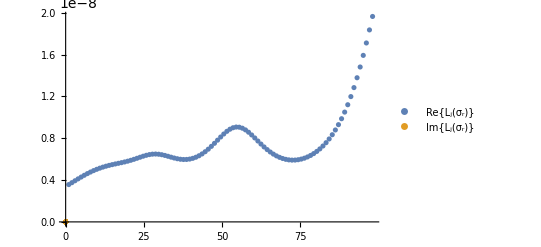

```mathematica
momentum=1;
sigmaI=12;
smin=1;smax=100;nbrs=100;
sigmaRange=Range[smin,smax,(smax-smin)/nbrs];

file="/home_th/kirscher/kette_repo/source/ComptonLIT/av18_deuteron/norm-ham-litME-"<>ToString[jj]<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];
ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="/home_th/kirscher/kette_repo/source/ComptonLIT/av18_deuteron/LIT_SOURCE_"<>ToString[jj]<>pi<>ToString[mJ]<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
(*Dimensions[norm];
Dimensions[ham];*)
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[momentum]];
lOfSigma={};
For[n=1,n<nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
lOfSigma=Append[lOfSigma,{sigmaRange[[n]],Conjugate[coeff].norm.coeff}];
)];
LIToverlap=Append[LIToverlap,lOfSigma];
lOfSigma;
Animate[ListPlot[{Re[lOfSigma],Im[lOfSigma]},PlotLegends->{"Re{L_j(σ_r)}","Im{L_j(σ_r)}"}],](*,PlotRange->{0,10^(-6)}]*)
```

```mathematica
ϕ=Pi/3;
θ=Pi/3;
Plot[Re[expandedState[r Cos[θ] Sin[ϕ],r Sin[θ] Sin[ϕ],r Cos[ϕ],Lsets[[jj+1]],basisWidths,coeff]],{r,.01,6.5}]
```

```mathematica
basisWidths//MatrixForm
```

({12.9567,5.13467,2.939,1.69017,0.843,0.257369,0.13852,0.038519}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011})

```mathematica
normmalcoeff=norm.coeff
normmalcoeff.coeff//MatrixForm
Conjugate[coeff].norm.coeff
```

{1.05785×10^-6+3.06049×10^-8 ⅈ,2.41402×10^-8+7.40847×10^-10 ⅈ,8.60316×10^-8+2.53363×10^-9 ⅈ,1.86044×10^-7+5.42301×10^-9 ⅈ,3.68715×10^-7+1.07022×10^-8 ⅈ,8.94637×10^-7+2.58962×10^-8 ⅈ}

1.36588×10^-12+7.91869×10^-14 ⅈ

1.36817×10^-12-1.31266×10^-27 ⅈ

```mathematica
ell=1;
m1=4;
m2=4;
(2 ell+1)!!/(2^(2+ell) (basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])^(1+ell)) Sqrt[Pi/(basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])]
```

0.0768279